```mathematica
line1s1s4=Import["lines/line_1S1S_L0_dim4.mx"];
line1s1s10=Import["lines/line_1S1S_L0_dim10.mx"];
line1s1s20=Import["lines/line_1S1S_L0_dim20.mx"];
omega=Table[{√(3/2),y},{y,3.67,3.70,0.01}];
eAnal=Table[{x,3.67423},{x,0.5,2.5,0.1}];
```

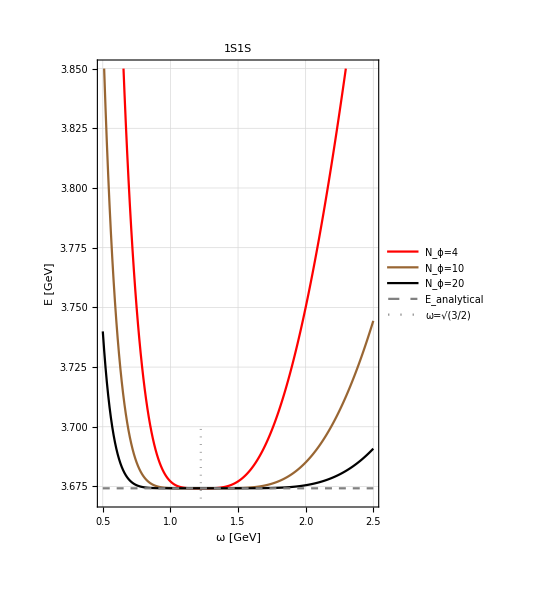

```mathematica
plot1=ListPlot[{line1s1s4,line1s1s10,line1s1s20,eAnal,omega},
Joined->True,
PlotRange->{{0.5,2.5},{3.67,3.85}},
PlotStyle->{Red,Brown,Black,{Gray,Dashed},{Gray,Dotted}},
AspectRatio->1.5,
PlotTheme->"Detailed",
PlotLabel->"1S1S",
PlotLegends->Placed[{"N_ϕ=4","N_ϕ=10","N_ϕ=20","E_analytical","ω=√(3/2)"},{Center,Top}],
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Times",FontSize->14}
]
```

```mathematica
Export["plots/thesis/ch4/ch4_equalM_1S1S_EvsW_new.pdf",plot1]
```

plots/thesis/ch4/ch4_equalM_1S1S_EvsW_new.pdf

```mathematica
line1s2s4=Import["lines/line_1S2S_L0_dim4.mx"];
line1s2s10=Import["lines/line_1S2S_L0_dim10.mx"];
line1s2s20=Import["lines/line_1S2S_L0_dim20.mx"];
omega=Table[{√(3/2),y},{y,6.0,6.5,0.1}];
eAnal=Table[{x,6.12372},{x,0.5,2.5,0.1}];
```

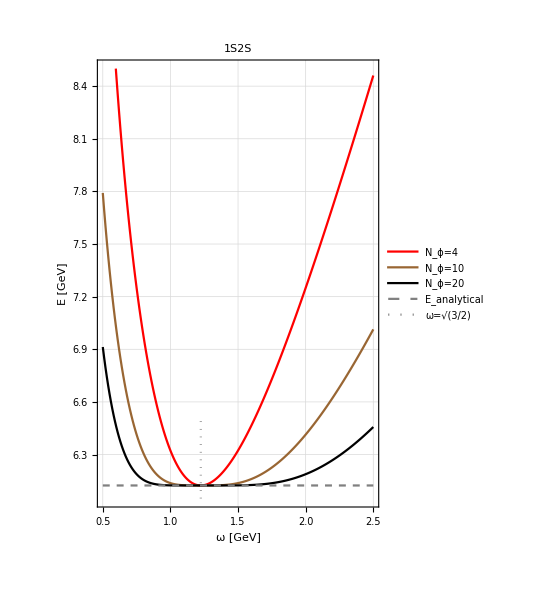

```mathematica
plot2=ListPlot[{line1s2s4,line1s2s10,line1s2s20,eAnal,omega},
Joined->True,
PlotRange->{{0.5,2.5},{6.05,8.5}},
PlotStyle->{Red,Brown,Black,{Gray,Dashed},{Gray,Dotted}},
AspectRatio->1.5,
PlotTheme->"Detailed",
PlotLabel->"1S2S",
PlotLegends->Placed[{"N_ϕ=4","N_ϕ=10","N_ϕ=20","E_analytical","ω=√(3/2)"},{Center,Top}],
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Times",FontSize->14}
]
```

```mathematica
Export["plots/thesis/ch4/ch4_equalM_1S2S_EvsW_new.pdf",plot2]
```

plots/thesis/ch4/ch4_equalM_1S2S_EvsW_new.pdf

```mathematica
line1d1d4=Import["lines/line_1D1D_L0_dim10.mx"];
line1d1d10=Import["lines/line_1D1D_L0_dim20.mx"];
line1d1d20=Import["lines/line_1D1D_L0_dim35.mx"];
omega=Table[{√(3/2),y},{y,8.5,9.0,0.1}];
eAnal=Table[{x,8.57321},{x,0.5,2.5,0.1}];
```

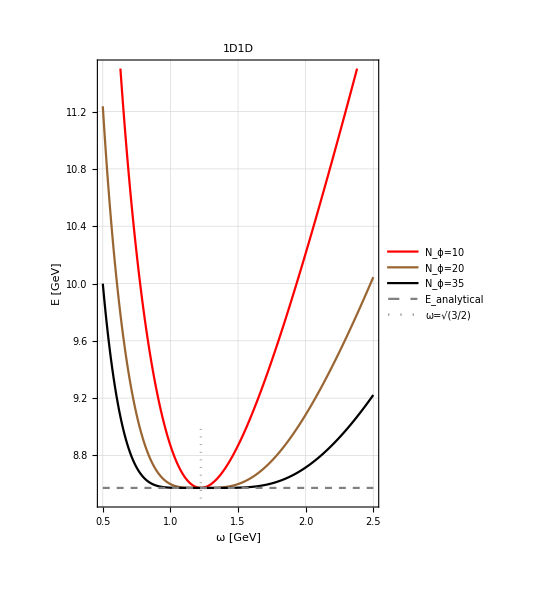

```mathematica
plot3=ListPlot[{line1d1d4,line1d1d10,line1d1d20,eAnal,omega},
Joined->True,
PlotRange->{{0.5,2.5},{8.5,11.5}},
PlotStyle->{Red,Brown,Black,{Gray,Dashed},{Gray,Dotted}},
AspectRatio->1.5,
PlotTheme->"Detailed",
PlotLabel->"1D1D",
PlotLegends->Placed[{"N_ϕ=10","N_ϕ=20","N_ϕ=35","E_analytical","ω=√(3/2)"},{Center,Top}],
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Times",FontSize->14}
]
```

```mathematica
Export["plots/thesis/ch4/ch4_equalM_1D1D_EvsW_new.pdf",plot3]
```

plots/thesis/ch4/ch4_equalM_1D1D_EvsW_new.pdf